```mathematica
DD[n_,k_] := DD[n,k]=Sum[DD[Floor[n/j],k-1],{j,1,n}]
DD[n_,1] := n
DD[n_,0] := 1
D2[n_,k_] := D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}]
D2[n_,1] := n-1
D2[n_,0] := 1
```

```mathematica
DD[100,2]
D2[100,2]
```

482

301

283

```mathematica
SN[n_,k_] := Sum[ (-1)^(j-1) DD[n,2 j - 1]/((2 j - 1 )!),{j,1,k}]
CS[n_,k_] := Sum[ (-1)^(j-1) DD[n,2 j - 2]/((2 j - 2 )!),{j,1,k}]
EE[n_,k_] := Sum[  DD[n,j]/( j!),{j,0,k}]
```

```mathematica
N[EE[100,11]]
```

825.274

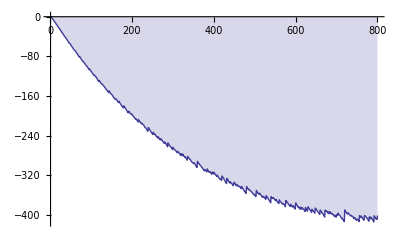

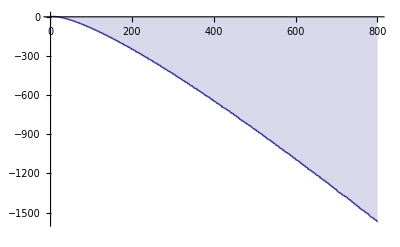

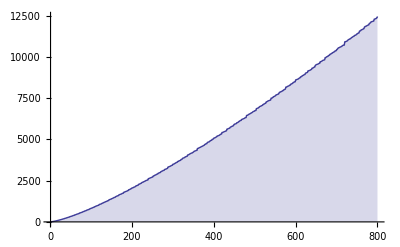

```mathematica
DiscretePlot[ CS[n,15],{n,1,800}]
DiscretePlot[ SN[n,15],{n,1,800}]
DiscretePlot[ EE[n,15],{n,1,800}]
```

```mathematica
Dx[0,a_,n_]:=1
Dx[k_,a_,n_]:=Sum[Binomial[k,j] Dx[k-j,m,n/m^j],{m,a+1,Floor[n^k^-1]},{j,1,k}]
NumberOfPrimes[n_]:=Sum[j^-1 MoebiusMu[j](-1)^(k+1) k^-1 Dx[k,1,n^j^-1],{j,1,Log[2,n]},{k,1,Log[2,n^j^-1]}]
```

```mathematica
NumberOfPrimes[1000]
```

168